## Import data files and create interpolation objects

Form factors span the range q = 1 to 2000 keV and E = 1 eV to 2 keV. 
q is the momentum transfer [in keV] and E is the electron kinetic energy [in keV].
Data is optimised for q = 1 to 500 keV and E = 1 eV to 1 keV. 
Interpolation outside this range is not accurate.
Outgoing electron wave functions are Coulomb waves with Zeff values from J. Chem. Phys. 38, 2686 (1963)

```mathematica
SetDirectory[NotebookDirectory[]];
LHe1sgrid=Import["He1s_CW_grid.dat"];
ResetDirectory[];

fHe1s=Interpolation[LHe1sgrid,InterpolationOrder->1]
```

InterpolatingFunction[…]

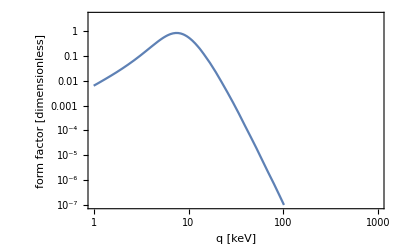

```mathematica
EtestkeV=0.025;

LogLogPlot[{fHe1s[q,EtestkeV]},{q,1,1000},PlotRange->{{1,1000},{10^-7,4}},Frame->True,FrameLabel->{"q [keV]","form factor [dimensionless]"}]
```

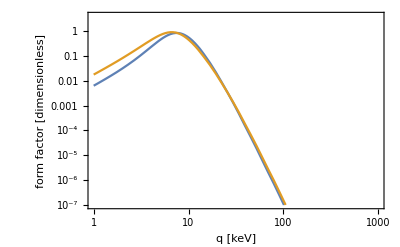

```mathematica
LogLogPlot[{fHe1s[q,EtestkeV],fHe1sSCH[q,EtestkeV]},{q,1,1000},PlotRange->{{1,1000},{10^-7,4}},Frame->True,FrameLabel->{"q [keV]","form factor [dimensionless]"}]
```

```mathematica
fHe1s[qkeV,EkeV]
```

0.553363

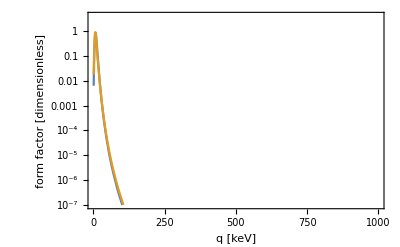

```mathematica
LogPlot[{fHe1s[q,EtestkeV],fHe1sSCH[q,EtestkeV]},{q,1,1000},PlotRange->{{1,1000},{10^-7,4}},Frame->True,FrameLabel->{"q [keV]","form factor [dimensionless]"}]
```